# Sosnova Pulse-Shaping Last Updated: 6/14/2021

```mathematica
Quit[]
```

```mathematica
Remove["Global`*"];ClearInOut[];
```

## 0 Prep

## 0.0 Setup

### 0.0.1 User Config

```mathematica
(*user input*)
	(*enter chain configuration*)
(*mArr={mMol,mMol};*)
```

```mathematica
mArr={mMol,mMol,mMol,mMol,mAtom};
```

### 0.0.2 Config - RDX

```mathematica
(*qubits*)
numIons=Length[mArr];
```

```mathematica
(*ion positions*)
indMol:=Position[mArr,mMol]//Flatten;
indAtom:=Position[mArr,mAtom]//Flatten;
```

### 0.0.3 Useful Functions

```mathematica
Off[General::munfl];
ParallelEvaluate[Off[General::munfl];];
```

LinkObject::linkw: Unable to write data to closed link ….

General::stop: Further output of LinkObject::linkw will be suppressed during this calculation.

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -pacletreadonly -wstp,124,4].

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -pacletreadonly -wstp,125,5].

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -pacletreadonly -wstp,126,6].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Parallel`Developer`ConnectKernel::failinit: 4 of 4 kernels failed to initialize.

```mathematica
(*play sound when finished*)
Done[type_:"none",msg_:""]:=With[{soundDJ=Play[Sin[600*π*t],{t,0,0.6}],message="Calc Done"},
Switch[type,
"text",SendMessage["SMS",message],
"email",SendMail[<|"To"->"claytonho@g.ucla.edu","Subject"->"Calc Done: "<>ToString[msg],"From"->"claytonho@physics.ucla.edu","Server"->"smtp.physics.ucla.edu","EncryptionProtocol"->"SSL","PortNumber"->465,"UserName"->"claytonho@physics.ucla.edu","Password"->"I2Ic1zIS2R"|>],
"none",EmitSound[soundDJ]];];
```

## 0.1 Values

### 0.1.1 Constants

```mathematica
(*fundamental*)
ℏ=1.0545718*^-34;me=9.10938356*^-31;qe=1.60217662*^-19;c=2.99792458*^8;kb=1.38064852*^-23;
```

```mathematica
(*derived*)
ke2=2.30707751*^-28;a0=ℏ^2/me/ke2;
```

```mathematica
(*defined*)
amu=1.66053904*^-27;wghz=2π 1.*^9;wmhz=2π 1.*^6;wkhz=2π 1.*^3;debye=1.*^-21/c;μs=1.*^-6;mm=1.*^-3;nm=1.*^-9;
```

### 0.1.2 Variables

```mathematica
(*mMol=38*amu;mAtom=40*amu;*)
```

```mathematica
mMol=171*amu;mAtom=138(*153.5*)*amu;
Δk=N[2*^9*2π/(mArr/.{mMol->355,mAtom->532})];
```

### 0.1.3 Quick Eigen

#### 0.1.3.1 in terms of ω_(sec-Mol), fixed ω_sec

```mathematica
wsecMol={3.06,0.16}*wmhz;
(*wsecMol={Sqrt[3.06^2+(0.16^2-#^2)/2],#}*wmhz&[1.116];
wsecMol/wmhz*)
```

```mathematica
wsecAtom:=(*√(mMol/mAtom)*){√((wsecMol[[1]]^2+(#)^2/2)*(mMol/mAtom)-(#)^2/2),#}&[wsecMol[[2]]];
```

```mathematica
wsecAtom/wmhz
```

{3.40673,0.16}

```mathematica
(*ωRF=40*wmhz;
qMol=2/ωRF √(2*wsecMol[[1]]^2+wsecMol[[2]]^2);qAtom=2/ωRF √(2*wsecAtom[[1]]^2+wsecAtom[[1]]^2);
qMol*)
```

#### 0.1.3.2 in terms of trap parameters

```mathematica
(*VRF=342.8;ωRF=28.25*wmhz;κr=1;r0=0.41278*mm;
z0=0.2*mm;κz=1;U=0.1433;
qMol:=(2*qe*(VRF*κr))/(mMol*ωRF^2*r0^2);qAtom:=(2*qe*(VRF*κr))/(mAtom*ωRF^2*r0^2);
wsecMol:=ωRF/2*Sqrt[{qMol^2/2-#,2.*#}]&[(4*qe*U*κz)/(z0^2*mMol*ωRF^2)];wsecAtom:=ωRF/2*Sqrt[{qAtom^2/2-#,2.*#}]&[(4*qe*U*κz)/(z0^2*mAtom*ωRF^2)];
wsecMol/wmhz*)
```

#### 0.1.3.3 Find Eigen

```mathematica
(*get individual secular frequencies*)
wsecvalsMAT=Transpose[mArr/.{mMol->wsecMol}/.{mAtom->wsecAtom}];
```

```mathematica
(*Calculate equilibrium positions (axial crystal)*)
z0eqArr = Array[z0eq,numIons];l0:=(ke2/(mMol*wsecMol[[2]]^2))^(1/3);
L0EQlist=z0eqArr[[#]]==(Sum[(z0eqArr[[#]] - z0eqArr[[k]])^(-2),{k,1,#-1}] - Sum[(z0eqArr[[#]] - z0eqArr[[k]])^(-2),{k, #+1,numIons}])&/@Range[numIons];
guessz0eq=Range[-#,#,2*#/(numIons-1)]&[numIons^(1/3)]//N;guessz0eq=Transpose[Join[{z0eqArr},{guessz0eq}]];
z0eqArr=z0eqArr/.Chop[FindRoot[L0EQlist,guessz0eq]];
(*z0eqArr/=2;*)
L0Mn=Abs[Table[If[i==j,0,(z0eqArr[[i]]-z0eqArr[[j]])^(-3)],{i,numIons},{j,numIons}]];
```

```mathematica
(*Create matrices*)
VMatZ=Table[Sqrt[mArr[[i]]/mArr[[j]]]*wsecvalsMAT[[2,i]]^2*If[i==j,1+2*Sum[L0Mn[[i,id]],{id,numIons}],-2*L0Mn[[i,j]]],{i,numIons},{j,numIons}];
VMatX=Table[Sqrt[mArr[[i]]/mArr[[j]]]*wsecvalsMAT[[2,i]]^2*If[i==j,(wsecvalsMAT[[1,i]]/wsecvalsMAT[[2,i]])^2-Sum[L0Mn[[i,id]],{id,numIons}],L0Mn[[i,j]]],{i,numIons},{j,numIons}];
(*get eigen*)
eigenholder={Eigensystem[VMatX],Eigensystem[VMatZ]};
wmvals=Sqrt[eigenholder[[;;,1]]];vmvals:=eigenholder[[;;,2]];
{vmvals[[#1]]//MatrixForm,wmvals[[#1]]/wmhz//MatrixForm}&[1]
```

{(0.000265351 | 0.000675013 | 0.00215682 | 0.0129131 | 0.999914
-0.631762 | -0.54766 | -0.450658 | -0.312766 | 0.00554856
0.67897 | -0.075047 | -0.476385 | -0.553499 | 0.00804605
-0.357343 | 0.674463 | 0.121726 | -0.634454 | 0.00757043
0.110377 | -0.489425 | 0.745079 | -0.439453 | 0.00436916),(3.40094
3.05884
3.05215
3.04352
3.03399)}

```mathematica
η[[1,1,;;]]*η[[1,5,;;]]
η[[1,2,;;]]*η[[1,5,;;]]
```

{1.01674×10^-6,-0.0000173661,0.0000273923,-0.0000137671,2.49364×10^-6}

{2.56866×10^-6,-0.0000150616,-2.99221×10^-6,0.0000259636,-0.0000110552}

```mathematica
η[[1,1,;;]]*η[[1,5,;;]]
η[[1,2,;;]]*η[[1,5,;;]]
```

{2.14607×10^-6,-0.0000315237,0.0000492365,-0.0000244506,4.37242×10^-6}

{5.45927×10^-6,-0.0000273271,-5.44214×10^-6,0.000046149,-0.0000193878}

```mathematica
(*wmvals={{3.403,3.062,3.056,3.048,3.039},{0.57,0.48,0.387,0.279,0.158}}*wmhz;*)
```

#### 0.1.3.4 Lamb-Dicke

```mathematica
η=√(ℏ/2.)Table[Δk[[i]]/(√(mArr[[i]]*wmvals[[d,q]]))*vmvals[[d,q,i]],{d,2},{i,numIons},{q,numIons}];
```

## 1 AM Pulse-Shaping

## 1.1 Setup

### 1.1.1 Pulse Shape

```mathematica
numPulses=5;pulseTime=200*μs;
```

```mathematica
pulseVec=Array[Ω,numPulses];
tArr=Range[0,pulseTime,pulseTime/numPulses];
```

### 1.1.2 Spin-Motion Conditions

```mathematica
Aim=Compile[{{u,_Real},{w,_Real},{η,_Real}},
(η/(u^2-w^2))*(#[[2;;-1]]-#[[;;-2]])&[Exp[ⅈ*w*tArr]*(u*Cos[u*tArr]-ⅈ*w*Sin[u*tArr])],CompilationTarget->"C"];
```

```mathematica
Bkl[u_Real,temp_,ions_List,dir_Integer]:=With[{AimMat={{Aim[u,wmvals[[dir,#]],η[[dir,ions[[1]],#]]]},{Aim[u,wmvals[[dir,#]],η[[dir,ions[[2]],#]]]}}&/@Range[numIons]},
0.25*(βk[temp,wmvals[[dir]]]).Apply[Plus,Map[ConjugateTranspose[#].#&,AimMat,{2}],1]]
```

### 1.1.3 Entanglement Conditions

```mathematica
(*functions for entanglement condition matrix*)
```

```mathematica
upper1f=Compile[{{up,_Real},{um,_Real}},
0.5*((up*Sin[um*tArr]-um*Sin[up*tArr])/(up*um)),CompilationTarget->"C"];
```

```mathematica
upper2f=Compile[{{up,_Real},{um,_Real}},
-0.5*((up Cos[um *tArr]+um Cos[up *tArr])/(up*um)),CompilationTarget->"C"];
```

```mathematica
diag1f=Compile[{{up,_Real},{um,_Real},{u,_Real},{w,_Real}},
0.25/(up*um)((2.*w*u*tArr+u Sin[2.*w*tArr]-w Sin[2.*u*tArr])/u-0.5*(um^2 Sin[2.*up*tArr]+up^2 Sin[2.*um*tArr])/(up*um)),CompilationTarget->"C"];
```

```mathematica
XklInd[u_,mode_,dir_]:=Module[
{upper1=upper1f[u+wmvals[[dir,mode]],u-wmvals[[dir,mode]]],
upper2=upper2f[u+wmvals[[dir,mode]],u-wmvals[[dir,mode]]],
diag1=diag1f[u+wmvals[[dir,mode]],u-wmvals[[dir,mode]],u,wmvals[[dir,mode]]],
upperMat,diagMat},
upperMat=(LowerTriangularize[Transpose[#1]-#1]&)[KroneckerProduct[upper1⟦2;;⟧-upper1⟦1;;-2⟧,upper2⟦2;;⟧-upper2⟦1;;-2⟧]];diagMat=(DiagonalMatrix[(#1⟦2;;All⟧+#1⟦1;;-2⟧) (#2⟦2;;⟧-#2⟦1;;-2⟧)-(#3⟦2;;⟧-#3⟦1;;-2⟧)]&)[upper1,upper2,diag1];(upperMat+diagMat)]
```

```mathematica
Xkl[u_,ions_List,dir_Integer]:=2.*Times@@η⟦dir,ions,Range[numIons]⟧.(XklInd[u,#1,dir]&)/@Range[numIons];
```

### 1.1.4 Temperature

```mathematica
(*phonon number*)
(*βk=Compile[{{temp,_Real},{w,_Real,1}},
Coth[3.81911755498*^-12*w/temp],CompilationTarget->"C"];*)
βk=Compile[{{temp,_Real},{w,_Real,1}},
Coth[7.63823510997*^-12*w/temp],CompilationTarget->"C"];
```

```mathematica
(*average phonon number*)
nAvg[temp_,wDJ_]:=(Exp[(ℏ*wDJ)/(kb*temp)]-1.)^-1;
```

### 1.1.5 Fidelity

```mathematica
(*for fidelity*)
```

```mathematica
Gi=Compile[{{u,_Real},{temp,_Real},{w,_Real,1},{η,_Real,1},{vec,_Complex,1}},
Exp[(-0.5*βk[temp,w]).Abs[(Aim[u,w[[#]],η[[#]]]&/@Range[numIons]).vec]^2]];
```

```mathematica
Gp=Compile[{{u,_Real},{temp,_Real},{w,_Real,1},{η1,_Real,1},{η2,_Real,1},{vec,_Complex,1}},
Exp[(-0.5*βk[temp,w]).Abs[((Aim[u,w[[#]],η1[[#]]]+Aim[u,w[[#]],η2[[#]]])&/@Range[numIons]).vec]^2]];
```

```mathematica
Gm=Compile[{{u,_Real},{temp,_Real},{w,_Real,1},{η1,_Real,1},{η2,_Real,1},{vec,_Complex,1}},
Exp[(-0.5*βk[temp,w]).Abs[((Aim[u,w[[#]],η1[[#]]]-Aim[u,w[[#]],η2[[#]]])&/@Range[numIons]).vec]^2]];
```

```mathematica
(*actual fidelity*)
Fid[u_,temp_,vec_,ions_,dir_]:=(0.25+0.25*(Gi[u,temp,wmvals[[dir]],η[[dir,ions[[1]]]],vec]+Gi[u,temp,wmvals[[dir]],η[[dir,ions[[2]]]],vec])+0.125(Gp[u,temp,wmvals[[dir]],η[[dir,ions[[1]]]],η[[dir,ions[[2]]]],vec]+Gm[u,temp,wmvals[[dir]],η[[dir,ions[[1]]]],η[[dir,ions[[2]]]],vec]));
```

## 1.2 Generalized Eigenvalue Problem

```mathematica
(*set values du jour*)
ionsDJ={1,5};dirDJ=1;uDJ=3.05416*wmhz;tempDJ=5.*^-5;
(*average n*)
1/(Exp[ℏ*wmvals[[1,1]]/kb/tempDJ]-1)
```

0.0270337

### 1.2.1 Optimize Fidelity

```mathematica
(*create matrices*)
DMat=0.5*(#+Transpose[#])&[Xkl[uDJ,ionsDJ,dirDJ]];
BMat=#+Transpose[#]&[Bkl[uDJ,tempDJ,ionsDJ,dirDJ]];
```

```mathematica
(*solve generalized eigenvalue problem*)
{eigenval,eigenvec}=Eigensystem[{BMat,DMat}]//Chop;
(*normalize eigenvectors*)
kNorm=Sqrt[π/4/(#.Xkl[uDJ,ionsDJ,dirDJ].#)]&/@eigenvec;
eigenvec*=kNorm;
```

```mathematica
(*(*remove invalid results*)
validres=Intersection[Position[Total[Abs[Re[eigenvec]],{2}],_?(#!=0&)]//Flatten,Position[Total[Abs[Im[eigenvec]],{2}],_?(#==0&)]//Flatten];
eigenval=eigenval[[validres]];eigenvec=eigenvec[[validres]];*)
```

```mathematica
kNorm
```

{3.25229×10^7,0.+3.21674×10^7 ⅈ,0.+4.99132×10^7 ⅈ,7.89463×10^6,5.02413×10^7}

### 1.2.2 Get Optimal Pulse Shape

```mathematica
(*get fidelities*)
fidDJ=Map[Fid[uDJ,tempDJ,#,ionsDJ,dirDJ]&,eigenvec]
(*best pulse shape*)
eigenvec[[First@Ordering[Abs[fidDJ],-1]]]/wkhz
eigenvec/wkhz//Chop//MatrixForm
```

{0.431201,0.426501,0.363779,0.499292,0.570776}

{-3418.2,4224.06,-2200.61,4237.35,-3407.9}

(2307. | -2827.61 | -9.5181 | 2853.55 | -2309.2
0.+1020.95 ⅈ | 0.-3038.91 ⅈ | 0.+2371.17 ⅈ | 0.-3048.22 ⅈ | 0.+1009.4 ⅈ
0.-3346.74 ⅈ | 0.+4034.77 ⅈ | 0.-2847.13 ⅈ | 0.+4050.45 ⅈ | 0.-3333.72 ⅈ
703.046 | 543.75 | 0.866254 | -550.799 | -696.705
-3418.2 | 4224.06 | -2200.61 | 4237.35 | -3407.9)

## 1.3 Sweep Detuning

```mathematica
(*set values du jour*)
ionsDJ={1,5};dirDJ=1;tempDJ=5*^-5;
(*average n*)
nAvg[tempDJ,wmvals[[1,1]]]
```

0.0270337

### 1.3.1 Encapsulation for Sweep

```mathematica
SweepFid[u_,temp_,ions_,dir_]:=Module[{XHolder=Xkl[u,ions,dir],eigenvec,fids},
eigenvec=Chop[Eigensystem[{#1+Transpose[#1],(#2+Transpose[#2])}]]&[Bkl[u,temp,ions,dir],XHolder][[2]];
eigenvec*=Abs[Sqrt[π/(4.*(#.(XHolder).#))]&/@eigenvec];
fids=Abs[Fid[u,temp,#,ions,dir]&/@eigenvec];
{fids[[#]],eigenvec[[#]]}&[First@Ordering[fids,-1]]]
```

### 1.3.2 Sweep

```mathematica
uArr=Range[#+3.0*wmhz,#+3.1*wmhz,0.01*wkhz]&[Sqrt[2*π]*π*ⅇ+Log[2]];uArr//Dimensions
AbsoluteTiming[usweepres=ParallelMap[SweepFid[#,tempDJ,ionsDJ,dirDJ]&,uArr];]
```

{10001}

{7.27219,Null}

{0.99998,6336,3.06335,749.196}

{449.888,{3.05717}}

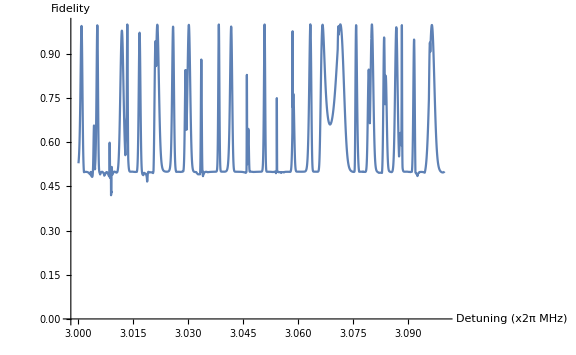
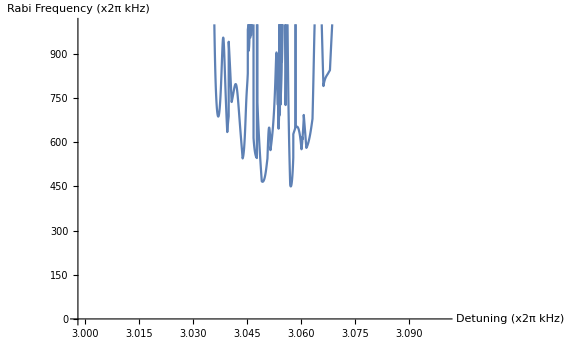

```mathematica
{Max[usweepres[[;;,1]]],#,Chop[(uArr[[#]](*-wmvals[[dirDJ,modeDJ]]*))/wmhz],Max[Abs[usweepres[[#,2]]]]/wkhz}&[First@Ordering[usweepres[[;;,1]],-1]]
{Min[#],uArr[[Ordering[#,1]]]/wmhz}&[Max/@Abs[usweepres[[;;,2]]/wkhz]]
{ListLinePlot[usweepres[[;;,1]],PlotRange->{0,1},DataRange->(uArr[[{1,-1}]])/wmhz,ImageSize->Large,AxesLabel->{"Detuning (x2π MHz)","Fidelity"}],ListLinePlot[Max/@Abs[usweepres[[;;,2]]/wkhz],DataRange->(uArr[[{1,-1}]])/wmhz,PlotRange->{0,1000},ImageSize->Large,AxesLabel->{"Detuning (x2π kHz)","Rabi Frequency (x2π kHz)"}]}
```

### 1.3.3 Process Sweep

```mathematica
usweepres2=Transpose[{uArr,usweepres[[;;,1]],(Max/@Abs[usweepres[[;;,2]]])}];
```

```mathematica
minfid=0.82;maxrabi=560*wkhz;
usweepProcessed=Select[usweepres2,#[[2]]>minfid&&#[[3]]<maxrabi&];
usweepProcessed//Length
```

4

```mathematica
usweepProcessed/ConstantArray[{wmhz,1,wkhz},Length[usweepProcessed]]//MatrixForm
```

(3.04768 | 0.826014 | 548.709
3.04769 | 0.842684 | 552.085
3.0477 | 0.859222 | 555.459
3.04771 | 0.875502 | 558.827)

## 2 Dual AM Shaping

## 2.1 Prep

### 2.1.1 Dual Pulse Shape

```mathematica
pulseVeci=Array[Ωi,numPulses];pulseVecj=Array[Ωj,numPulses];
```

### 2.1.2 Spin-Motion Conditions

```mathematica
Bkl2[u_,temp_,ion_,dir_]:=With[{AimMat={Aim[u,wmvals[[dir,#]],η[[dir,ion,#]]]}&/@Range[numIons]},
0.25*(βk[temp,wmvals[[dir]]]).(Map[ConjugateTranspose[#].#&,AimMat])]
```

### 2.1.3 Fidelity

```mathematica
(*actual fidelity*)
Fid2[u_,temp_,veci_,vecj_,ions_,dir_]:=1/8*(2+2*(Gi[u,temp,veci,ions[[1]],dir]+Gi[u,temp,vecj,ions[[2]],dir])+(Gp2[u,temp,veci,vecj,ions,dir]+Gm2[u,temp,veci,vecj,ions,dir]));
```

```mathematica
(*for fidelity*)
```

```mathematica
Gp2=Compile[{{u,_Real},{temp,_Real},{w,_Real,1},{η1,_Real,1},{η2,_Real,1},{veci,_Complex,1},{vecj,_Complex,1}},
Exp[(-0.5*βk[temp,w]).Abs[(Aim[u,w[[#]],η1[[#]]].veci+Aim[u,w[[#]],η2[[#]]].vecj)&/@Range[numIons]]^2]];
```

```mathematica
Gm2=Compile[{{u,_Real},{temp,_Real},{w,_Real,1},{η1,_Real,1},{η2,_Real,1},{veci,_Complex,1},{vecj,_Complex,1}},
Exp[(-0.5*βk[temp,w]).Abs[(Aim[u,w[[#]],η1[[#]]].veci-Aim[u,w[[#]],η2[[#]]].vecj)&/@Range[numIons]]^2]];
```

```mathematica
(*actual fidelity*)
Fid2[u_,temp_,veci_,vecj_,ions_,dir_]:=(0.25+0.25*(Gi[u,temp,wmvals[[dir]],η[[dir,ions[[1]]]],veci]+Gi[u,temp,wmvals[[dir]],η[[dir,ions[[2]]]],vecj])+0.125(Gp2[u,temp,wmvals[[dir]],η[[dir,ions[[1]]]],η[[dir,ions[[2]]]],veci,vecj]+Gm2[u,temp,wmvals[[dir]],η[[dir,ions[[1]]]],η[[dir,ions[[2]]]],veci,vecj]));
```

## 2.2 Generalized Eigenvalue Problem

```mathematica
(*set values du jour*)
ionsDJ={1,5};dirDJ=1;uDJ=3.05558*wmhz;tempDJ=5*^-5;
```

### 2.2.1 Optimize Fidelity

```mathematica
(*create matrices*)
DMat2=ArrayFlatten[{{0,#+Transpose[#]},{#+Transpose[#],0}}]&[Xkl[uDJ,ionsDJ,dirDJ]];
BMat2=ArrayFlatten[{{#1+Transpose[#1],0},{0,#2+Transpose[#2]}}]&[Bkl2[uDJ,tempDJ,ionsDJ[[1]],dirDJ],Bkl2[uDJ,tempDJ,ionsDJ[[2]],dirDJ]];
```

```mathematica
(*solve generalized eigenvalue problem*)
eigenvec2=Chop[Eigensystem[{BMat2,DMat2}][[2]]];
kNorm2=Sqrt[π/(2.*(#.DMat2.#))]&/@eigenvec2;
eigenvec2=Chop[eigenvec2*kNorm2,1*^-3];
```

```mathematica
eigenvec2/wkhz//MatrixForm
```

(122.308 | 12.9384 | -0.624542 | -11.3822 | -123.808 | 24252. | 2988.45 | -2.94163 | -2979.26 | -24278.6
0.+122.308 ⅈ | 0.+12.9384 ⅈ | 0.-0.624542 ⅈ | 0.-11.3822 ⅈ | 0.-123.808 ⅈ | 0.-24252. ⅈ | 0.-2988.45 ⅈ | 0.+2.94163 ⅈ | 0.+2979.26 ⅈ | 0.+24278.6 ⅈ
-41.561 | 47.7253 | -29.53 | 42.857 | -37.7039 | 4714.61 | -4373.72 | 4279.81 | -4272.87 | 5472.55
0.-41.561 ⅈ | 0.+47.7253 ⅈ | 0.-29.53 ⅈ | 0.+42.857 ⅈ | 0.-37.7039 ⅈ | 0.-4714.61 ⅈ | 0.+4373.72 ⅈ | 0.-4279.81 ⅈ | 0.+4272.87 ⅈ | 0.-5472.55 ⅈ
21.6871 | 9.58163 | -59.0806 | 38.719 | -0.0893998 | -3554.28 | -5189.06 | 4459.44 | -5266.14 | -3312.04
0.-21.6871 ⅈ | 0.-9.58163 ⅈ | 0.+59.0806 ⅈ | 0.-38.719 ⅈ | 0.+0.0893998 ⅈ | 0.-3554.28 ⅈ | 0.-5189.06 ⅈ | 0.+4459.44 ⅈ | 0.-5266.14 ⅈ | 0.-3312.04 ⅈ
0.-69.2979 ⅈ | 0.+96.2905 ⅈ | 0.-2.16484 ⅈ | 0.-93.4799 ⅈ | 0.+72.6586 ⅈ | 0.-1702.9 ⅈ | 0.+2795.32 ⅈ | 0.-597.41 ⅈ | 0.-1448.03 ⅈ | 0.+2984.78 ⅈ
-69.2979 | 96.2905 | -2.16484 | -93.4799 | 72.6586 | 1702.9 | -2795.32 | 597.41 | 1448.03 | -2984.78
98.9632 | 62.1406 | -63.0738 | 65.8106 | 96.2858 | 922.745 | 986.06 | 1178.75 | 922.472 | 954.336
0.+98.9632 ⅈ | 0.+62.1406 ⅈ | 0.-63.0738 ⅈ | 0.+65.8106 ⅈ | 0.+96.2858 ⅈ | 0.-922.745 ⅈ | 0.-986.06 ⅈ | 0.-1178.75 ⅈ | 0.-922.472 ⅈ | 0.-954.336 ⅈ)

```mathematica
(*throw away duplicates*)
validres=Position[Total[Abs[Im[eigenvec2]],{2}],_?(#==0&)]//Flatten;
eigenvec2=eigenvec2[[validres]];
```

### 2.2.2 Get Optimal Pulse Shape

```mathematica
(*get fidelities*)
fidDJ2=Map[Fid2[uDJ,tempDJ,#[[;;numPulses]],#[[numPulses+1;;]],ionsDJ,dirDJ]&,eigenvec2]
(*best pulse shape*)
eigenvec2[[First@Ordering[Abs[fidDJ2],-1]]]/wkhz
{eigenvec2[[;;,;;numPulses]]/wkhz//Chop//MatrixForm,eigenvec2[[;;,numPulses+1;;]]/wkhz//Chop//MatrixForm}
```

{0.252314,0.748189,0.901627,0.984418,0.992288}

{98.9632,62.1406,-63.0738,65.8106,96.2858,922.745,986.06,1178.75,922.472,954.336}

{(122.308 | 12.9384 | -0.624542 | -11.3822 | -123.808
-41.561 | 47.7253 | -29.53 | 42.857 | -37.7039
21.6871 | 9.58163 | -59.0806 | 38.719 | -0.0893998
-69.2979 | 96.2905 | -2.16484 | -93.4799 | 72.6586
98.9632 | 62.1406 | -63.0738 | 65.8106 | 96.2858),(24252. | 2988.45 | -2.94163 | -2979.26 | -24278.6
4714.61 | -4373.72 | 4279.81 | -4272.87 | 5472.55
-3554.28 | -5189.06 | 4459.44 | -5266.14 | -3312.04
1702.9 | -2795.32 | 597.41 | 1448.03 | -2984.78
922.745 | 986.06 | 1178.75 | 922.472 | 954.336)}

## 2.3 Sweep Detuning

```mathematica
(*set values du jour*)
ionsDJ={1,5};dirDJ=1;tempDJ=5*^-5;
```

### 2.3.1 Encapsulation for Sweep

```mathematica
SweepFid2[u_,temp_,ions_,dir_]:=Module[
{DMatDJ=0.5*ArrayFlatten[{{0,#+Transpose[#]},{#+Transpose[#],0}}]&[Xkl[u,ions,dir]],
BMatDJ=0.5*ArrayFlatten[{{#1+Transpose[#1],0},{0,#2+Transpose[#2]}}]&[Bkl2[u,temp,ions[[1]],dir],Bkl2[u,temp,ions[[2]],dir]],
eigenvec,validres,fids},
eigenvec=Chop[Eigensystem[{BMatDJ,DMatDJ}]][[2]];
eigenvec*=Chop[Sqrt[π/(4.*(#.DMatDJ.#))]&/@eigenvec,1*^-3];
fids=Map[Fid2[u,temp,#[[;;numPulses]],#[[numPulses+1;;]],ions,dir]&,eigenvec];
{fids[[#]],Abs[eigenvec[[#]]]}&[Ordering[Abs[fids]][[-1]]]];
```

### 2.3.2 Sweep Prep

```mathematica
uArr=Range[#+3.05557*wmhz,#+3.05564*wmhz,0.0001*wkhz]&[Sqrt[7*Sqrt[π]]*0.2*Exp[π]*ⅇ+Log[2]];uArr//Dimensions
AbsoluteTiming[usweepres=ParallelMap[SweepFid2[#,tempDJ,ionsDJ,dirDJ]&,uArr];]
```

{701}

{0.901939,Null}

{0.99255,1,3.05558,{100.632,1159.84}}

{100.632,63.3793,64.2314,66.8156,98.1315,906.192,964.131,1159.84,906.071,932.792}

{1159.84,{3.05558}}

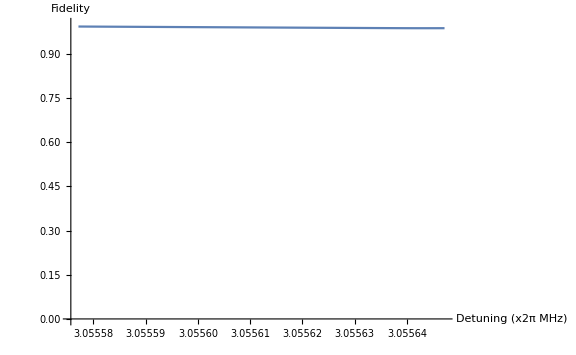
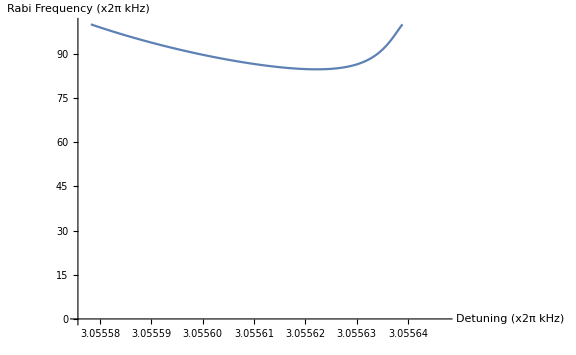
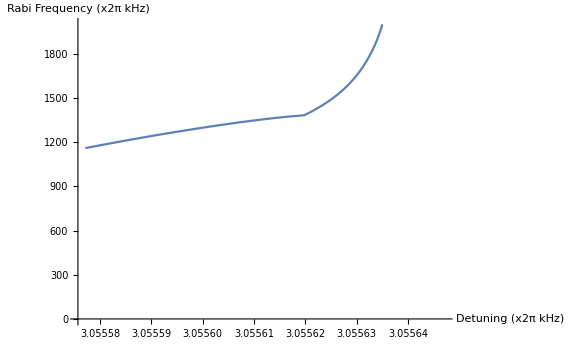

```mathematica
{Max[usweepres[[;;,1]]],#,Chop[(uArr[[#]])/wmhz],{Max[Abs[usweepres[[#,2,;;numPulses]]]]/wkhz,Max[Abs[usweepres[[#,2,numPulses+1;;]]]]/wkhz}}&[First@Ordering[usweepres[[;;,1]],-1]]
usweepres[[%[[2]],2]]/wkhz
{Min[#],uArr[[Ordering[#,1]]]/wmhz}&[Max/@Abs[usweepres[[;;,2]]/wkhz]]
{ListLinePlot[usweepres[[;;,1]],DataRange->(uArr[[{1,-1}]])/wmhz,PlotRange->{0,1},ImageSize->Large,AxesLabel->{"Detuning (x2π MHz)","Fidelity"}],ListLinePlot[Max/@Abs[usweepres[[;;,2,;;numPulses]]/wkhz],DataRange->(uArr[[{1,-1}]])/wmhz,PlotRange->{0,100},ImageSize->Large,AxesLabel->{"Detuning (x2π kHz)","Rabi Frequency (x2π kHz)"}],
ListLinePlot[Max/@Abs[usweepres[[;;,2,numPulses+1;;]]/wkhz],DataRange->(uArr[[{1,-1}]])/wmhz,PlotRange->{0,2000},ImageSize->Large,AxesLabel->{"Detuning (x2π kHz)","Rabi Frequency (x2π kHz)"}]}
```

### 2.3.3 Process Sweep

```mathematica
usweepres2=Transpose[{uArr,usweepres[[;;,1]],(Max/@Abs[usweepres[[;;,2,;;numPulses]]]),(Max/@Abs[usweepres[[;;,2,numPulses+1;;]]])}];
```

```mathematica
minfid=0.9;maxrabi1=100*wkhz;maxrabi2=1170*wkhz;
usweepProcessed=Select[usweepres2,#[[2]]>minfid&&#[[3]]<maxrabi1&&#[[4]]<maxrabi2&];
usweepProcessed//Length
```

5

```mathematica
usweepProcessed/ConstantArray[{wmhz,1,wkhz,wkhz},Length[usweepProcessed]]//MatrixForm
```

(3.05558 | 0.992448 | 99.9733 | 1167.23
3.05558 | 0.992439 | 99.9141 | 1167.9
3.05558 | 0.99243 | 99.8551 | 1168.57
3.05558 | 0.992421 | 99.7962 | 1169.23
3.05558 | 0.992412 | 99.7374 | 1169.9)

## 3 AM-FM Gates

## 3.1 Prep

### 3.1.1

```mathematica
(*cost function*)
cost[θ_]:=Sum[(NIntegrate[Exp[ⅈ*#],{t,0,tArr[[-1]]}])^2&[Integrate[θ[t1],{t1,0,t}]],{k,numIons}]
```

```mathematica
(*FM pulse shape*)
```

## 3.2 Optimization